#### random

{4,2,2,3,2,1,5,6,1,4,4,2,1,2,«72»,2,4,6,2,6,2,5,5,1,3,2,6,5,1}

{1→15,2→26,3→11,4→15,5→15,6→18}

{3/20,13/50,11/100,3/20,3/20,9/50}

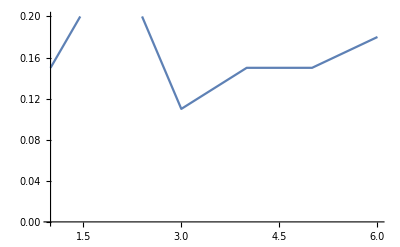

```mathematica
pln=100;
plt=RandomInteger[{1,6},pln];Short@plt
pct=SortBy[Normal@Counts@plt,First]
pctN=#[[2]]/pln&/@(List@@#&/@pct)
ListLinePlot[pctN,PlotRange->{{1,6},{0,.2}}]
```

#### white noise

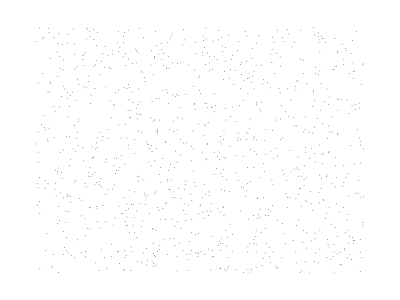

```mathematica
pts={RandomInteger[600],RandomInteger[450]}&/@Range@1000;
Framed@Graphics[{PointSize[.001],Point@pts}]
```

#### brownian motion

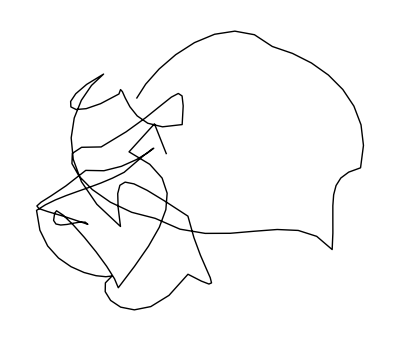

```mathematica
Graphics[{Thin,BezierCurve@Accumulate@RandomReal[{-1,1},{60,2}]}]
```

#### make sense

```mathematica
pln=1000;
series=RandomInteger[{1,6},{pln,3}];
Short@%
```

{{4,1,2},{6,4,6},{2,3,1},«994»,{6,4,3},{2,6,4},{1,5,4}}

{7,16,6,17,13,10,10,13,8,6,«980»,17,11,14,13,11,10,13,13,12,10}

{3→5,4→15,5→19,6→37,7→69,8→101,9→112,10→121,11→121,12→113,13→101,14→87,15→47,16→33,17→12,18→7}

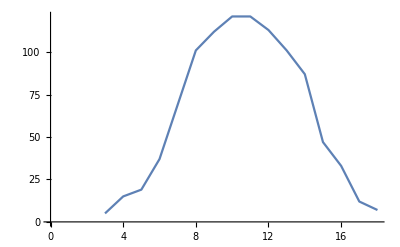

```mathematica
tot=Total/@series;Short@tot
counts=SortBy[Normal@Counts@tot,First]
ListLinePlot[List@@@counts]
```

```mathematica
BR2[len_,rot_,ite_]:=Module[{},If[ite==0,Return[]];
{Line[{{0,0},{0,len}}],Translate[{Rotate[{BR2[LinkLength@len,rot,ite-1]},LinkRotation@rot,{0,0}],Rotate[{BR2[LinkLength@len,rot,ite-1]},-LinkRotation@rot,{0,0}]},{0,len}]}]
δ1=NormalDistribution[2,.1];
δ2=NormalDistribution[6,1];
LinkLength[len_]:=len/RandomVariate@δ1
LinkRotation[rot_]:=π/RandomVariate@δ2
tree:=Graphics[BR2[1,π/6,6],PlotRange->{{-.9,.9},{0,2.2}},ImageSize->64]
Grid@Partition[Table[tree,{i,1,16}],4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
mean=Mean@tot
```

5341/500

```mathematica
sDev=StandardDeviation@plt
```

(√(30451/11))/30

```mathematica
nd=PDF[NormalDistribution[mean,sDev],x]
```

15 ⅇ^(-(4950 (-5341/500+x)^2)/30451) √(22/(30451 π))

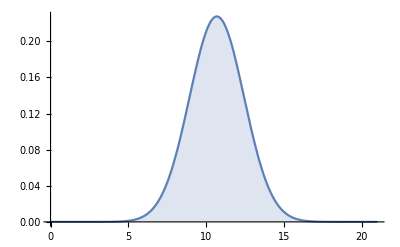

```mathematica
Plot[nd//Evaluate,{x,0,21},Filling->Axis]
```

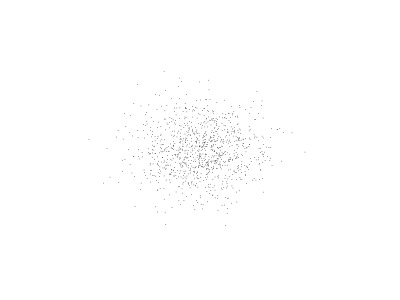

```mathematica
pts=RandomVariate[NormalDistribution[0,.1],2] {600,450}&/@Range@1000;
Framed@Graphics[{PointSize[.001],Point@pts},PlotRange->{{-300,300},{-225,225}}]
```

### MARKOV chain

```mathematica
series={1,2,1,1,2,1,2,3,2,1,1,2,3,1,2};
```

```mathematica
states=DeleteDuplicates@series
```

{1,2,3}

```mathematica
transitions=Partition[series,2,1]
```

{{1,2},{2,1},{1,1},{1,2},{2,1},{1,2},{2,3},{3,2},{2,1},{1,1},{1,2},{2,3},{3,1},{1,2}}

```mathematica
follow=#[[2]]&/@Extract[transitions,Position[transitions,{#,_}]]&/@states
```

{{2,1,2,2,1,2,2},{1,1,3,1,3},{2,1}}

```mathematica
C1[fol_,states_]:=(Length@Position[fol,#]&/@states)/Length@fol
pm=C1[#,states]&/@follow
```

{{2/7,5/7,0},{3/5,0,2/5},{1/2,1/2,0}}

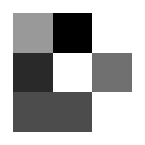

```mathematica
ArrayPlot@pm
```

```mathematica
P=DiscreteMarkovProcess[1,pm];
```

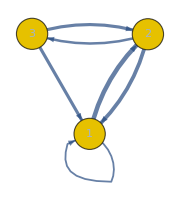

```mathematica
el=Flatten@Table[DirectedEdge[i,j]->Thickness[pm[[i,j]]/40],{i,Length@pm},{j,Length@pm}];
eld=Delete[el,Position[el,_->Thickness[0]]];
Graph[DiscreteMarkovProcess[1,pm],EdgeStyle->eld,ImageSize->Small]
```

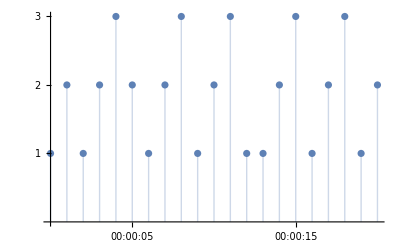

```mathematica
data=RandomFunction[P,{0,20}];
ListPlot[data,Filling->Axis,Ticks->{Automatic,{1,2,3}}]
```

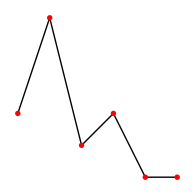

```mathematica
pts={{0,0},{1,3},{2,-1},{3,0},{4,-2},{5,-2}};
Graphics[{Line[pts],Red,PointSize@.02,Point[pts]}]
```

3.22135×10^-13+22.1 x-32.4167 x^2+16.625 x^3-3.58333 x^4+0.275 x^5

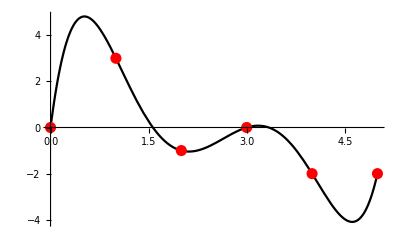

```mathematica
lm6=Fit[pts,x^#&/@Range[0,5],x]
Show[Plot[lm6,{x,0,5},PlotStyle->Black],Graphics[{Red,PointSize@.02,Point[pts]}]]
```

2.22976×10^-13+12.1 x-19.5833 x^2+10.7083 x^3-2.41667 x^4+0.191667 x^5

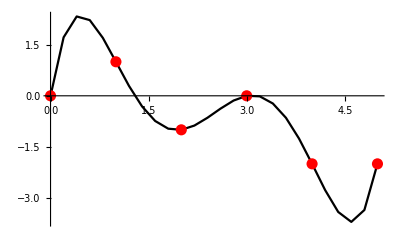

```mathematica
lm6=Fit[pts,x^#&/@Range[0,5],x]
Show[DiscretePlot[lm6,{x,0,5,.2},PlotStyle->Black,Filling->None,Joined->True],Graphics[{Red,PointSize@.02,Point[pts]}]]
```

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,-2}};
Graphics[{BSplineCurve[pts],Red,PointSize@.02,Point[pts]}]
```

-Graphics-

### CNN

```mathematica
nm = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

### floorplans